```mathematica
(*
e[x]_here = e_1(x)_{Lagrangian approach};
v[x]_here = {v^1(x)}_{Lagrangian approach};
σ[x]_here  = σ(x)_{Lagrangian approach};
*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
ϵ[1]=1;
```

```mathematica
ass={ψ[x]∈Reals,ν[x]>0};
```

```mathematica
e[x_]:=ν[x]{Cos[ψ[x]],-Sin[ψ[x]]}
```

```mathematica
n[x_]:={-e[x][[2]],e[x][[1]]}/Norm[e[x]]
```

```mathematica
g[x_]:=Simplify[{{e[x].e[x]}},Assumptions->ass]
```

```mathematica
sqrtdetg[x_]:=Sqrt[Det[g[x]]]
```

```mathematica
gc[x_]:=Inverse[g[x]]
```

```mathematica
FullSimplify[{{-n'[x].e[x]}},Assumptions->ass]
```

{{-ν[x] ψ'[x]}}

```mathematica
b[x_]:={{-ν[x] ψ'[x]}}
```

```mathematica
1/2FullSimplify[Sum[gc[x][[i,j]]b[x][[j,i]],{i,1,1},{j,1,1}],Assumptions->ass]
```

-ψ'[x]/(2 ν[x])

```mathematica
H[x_]:=-ψ'[x]/(2 ν[x])
```

```mathematica
K[x_]:=0
```

```mathematica
Γ[x_]:=ResourceFunction["ChristoffelSymbol"][g[x],{x}] //FullSimplify
```

```mathematica
Γ[x]
```

{{{ν'[x]/ν[x]}}}

```mathematica
(* \Nabla_k f_i*)
```

```mathematica
Nablaf[f_][i_,k_][x_]:=Derivative[ϵ[k]][f[i]][x]-Sum[f[j][x] Γ[x][[j,i,k]],{j,1,1}]
```

```mathematica
(*\Nabla_k v^i*)
```

```mathematica
Nablav[v_][i_,k_][x_]:=Derivative[ϵ[k]][v[i]][x]+Sum[v[j][x] Γ[x][[i,j,k]],{j,1,1}]
```

```mathematica
(*Nabla_k t^{il}*)
```

```mathematica
Nablavv[t_][i_,l_,k_][x_]:=Derivative[ϵ[k]][t[i,l]][x]+Sum[t[j,l][x] Γ[x][[i,j,k]],{j,1,1}]+Sum[t[i,j][x] Γ[x][[l,j,k]],{j,1,1}]
```

```mathematica
dH[1][x_]:=H'[x]
```

```mathematica
(*expression for Nabla_i Nabla^i H*)
```

```mathematica
FullSimplify[Sum[gc[x][[i,j]]Nablaf[dH][i,j][x],{i,1,1},{j,1,1}],Assumptions->ass]
```

(-3 ν'[x]^2 ψ'[x]+3 ν[x] ν'[x] ψ''[x]+ν[x] (ψ'[x] ν''[x]-ν[x] ψ^(3)[x]))/(2 ν[x]^5)

```mathematica
NabNabH[x_]:=(-3 ν'[x]^2 ψ'[x]+3 ν[x] ν'[x] ψ''[x]+ν[x] (ψ'[x] ν''[x]-ν[x] Derivative[3][ψ][x]))/(2 ν[x]^5)
```

```mathematica
(*auxiliary definition to obtain the covariant derivatives of v*)
```

```mathematica
vv[1][x_]:=v[x]
```

```mathematica
FullSimplify[Nablav[vv][1,1][x],Assumptions->ass]
```

v'[x]+(v[x] ν'[x])/ν[x]

```mathematica
(*Nablaivi = Nabla_i v^i*)
```

```mathematica
Nablaivi[x_]:=FullSimplify[Nablav[vv][1,1][x],Assumptions->ass]
```

```mathematica
(*rate-of-deformation tensor d^{ij}*)
```

```mathematica
dc[1,1][x_]:=gc[x][[1,1]]Nablav[vv][1,1][x]-w[x]gc[x][[1,1]]gc[x][[1,1]]b[x][[1,1]]
```

```mathematica
eqv=FullSimplify[ρ(v[x]Nablaivi[x]-2 v[x]w[x] gc[x][[1,1]]b[x][[1,1]]-w[x] gc[x][[1,1]]w'[x])
-gc[x][[1,1]]σ'[x]
-2 η Nablavv[dc][1,1,1][x]==0,Assumptions->ass];
eqσ=FullSimplify[Nablaivi[x]-2 H[x]w[x]==0,Assumptions->ass];
eqψ=FullSimplify[{ρ v[x](v[x]b[x][[1,1]]+w'[x])
-κ( - 2 NabNabH[x]-4H[x](H[x]^2-K[x]))
-2 σ[x]H[x]
- 2η( Nablaivi[x] gc[x][[1,1]]b[x][[1,1]]-2 w[x]*(2 H[x]^2-K[x]))==0},Assumptions->ass];
eqX={X1'[x]==ν[x] Cos[ψ[x]],X2'[x]==-ν[x] Sin[ψ[x]]};
```

```mathematica
eqv
```

v[x] (ρ ν[x]^4 v'[x]+ρ v[x] ν[x]^3 ν'[x]+2 η ν'[x]^2+2 ρ w[x] ν[x]^5 ψ'[x]-2 η ν[x] ν''[x])==ν[x] (ν[x] σ'[x]+2 η (v'[x] ν'[x]+w'[x] ψ'[x]+ν[x] v''[x]))+w[x] (ρ ν[x]^2 w'[x]-2 η ν'[x] ψ'[x]+2 η ν[x] ψ''[x])

```mathematica
(* given that I am at steady state, it must be w[x]=0, thus I simplify the equations by setting *)
```

```mathematica
w[x_]:=0
```

```mathematica
eqσ
```

ν[x] v'[x]+v[x] ν'[x]==0

```mathematica
(*
eqσ implies that ν[x] * v[x] = const., thus  

v[x]=A/ν[x];
  v[xmin]=A/ν[xmin];
  A= v[xmin] * ν[xmin];
thus
v[x]=v[xmin] * ν[xmin]/ν[x]
*)
```

```mathematica
repv={v[x]->A/ν[x],v'[x]->-(A ν'[x])/ν[x]^2,v''[x]->(A (2 ν'[x]^2-ν[x] ν''[x]))/ν[x]^3};
```

```mathematica
(*the boundary condition n_i Pi^{ij} = 0 at partial_Omega_r is automatically satisfied by the solution for v given by repv*)
```

```mathematica
dc[1,1][x]/.repv
```

0

```mathematica
FullSimplify[eqv/.repv]
```

ν[x] σ'[x]==0

```mathematica
(*eqv thus implies that σ[x]= σc*)
```

```mathematica
σ[x_]:=σc
```

```mathematica
(*we thus reduce the original problem for v,w,σ,ψ,X to a reduced problem for ψ and X only*)
```

```mathematica
(*the boundary conditions and differential equations for the reduced problem are*)
```

```mathematica
bcs={
ψ[xmin]==ψmin,ψ[xmax]==ψmax,ψ'[xmin]==ψpmin,
X1[xmin]==X1min,X2[xmin]==X2min};
```

```mathematica
eqs=Flatten[{eqψ,eqX}/.repv]
```

{2 A^2 ρ ν[x]^4 ψ'[x]+ψ'[x] (6 κ ν'[x]^2+ν[x] (ν[x] ψ'[x] ((4 A η σc ν'[x])/ν[x]+κ ψ'[x])-2 κ ν''[x]))+2 κ ν[x]^2 ψ^(3)[x]==2 ν[x] (2 A η σc ν'[x] ψ'[x]^2+3 κ ν'[x] ψ''[x]),X1'[x]==Cos[ψ[x]] ν[x],X2'[x]==-Sin[ψ[x]] ν[x]}

```mathematica
(*parameters*)
```

```mathematica
κ=1;
ρ=1;
η=1;
xmin=1;
xmax=3;
vmin=1;
A=vmin*ν[xmin];
σc=0;
ψmin=-1/2;
ψmax=2;
ψpmin=-1;
X1min=0;
X2min=0;
```

```mathematica
bcs
```

{ψ[1]==-1/2,ψ[3]==2,ψ'[1]==-1,X1[1]==0,X2[1]==0}

```mathematica
(*ν[x_]:=1*)
```

```mathematica
ν[x_]:=x/(1+x)
```

```mathematica
s=NDSolve[FullSimplify[Flatten[{eqs,bcs}]],{ψ,X1,X2},{x,xmin,xmax}][[1]]
```

{ψ→InterpolatingFunction[…],X1→InterpolatingFunction[…],X2→InterpolatingFunction[…]}

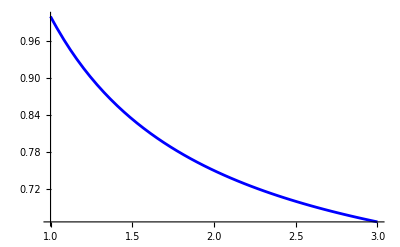

```mathematica
plotvexact=Plot[v[x]/.repv/.s,{x,xmin,xmax},PlotStyle->Blue]
```

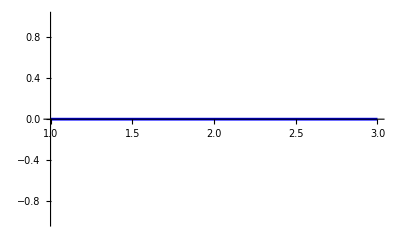

```mathematica
plotwexact=Plot[w[x],{x,xmin,xmax},PlotStyle->Blue]
```

```mathematica
plotσexact=Plot[σ[x]/.s,{x,xmin,xmax},PlotStyle->Blue]
```

-Graphics-

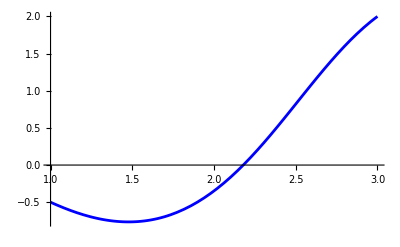

```mathematica
plotψexact=Plot[ψ[x]/.s,{x,xmin,xmax},PlotStyle->Blue]
```

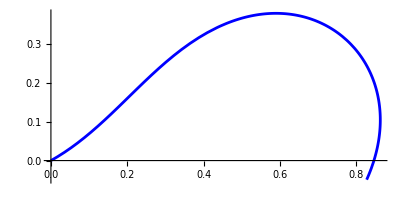

```mathematica
plotXexact=ParametricPlot[{X1[x],X2[x]}/.s,{x,xmin,xmax},PlotStyle->Blue]
```

```mathematica
(*check FE solution*)
```

```mathematica
(*check v*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/v.csv"];
t=Table[{t[[i,4]],t[[i,1]]},{i,2,Length[t]}]
```

{{3.,0.666667},{2.9,0.672414},{2.8,0.678571},{2.7,0.685185},{2.6,0.692308},{2.5,0.7},{2.4,0.708333},{2.3,0.717391},{2.2,0.727273},{2.1,0.738095},{2.,0.75},{1.9,0.763158},{1.8,0.777778},{1.7,0.794118},{1.6,0.8125},{1.5,0.833333},{1.4,0.857143},{1.3,0.884616},{1.2,0.916667},{1.1,0.954546},{1.,1.}}

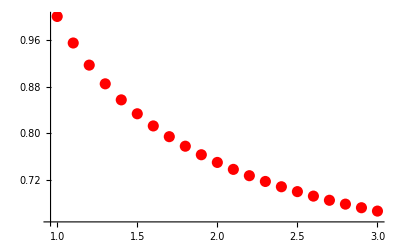

```mathematica
plotvnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

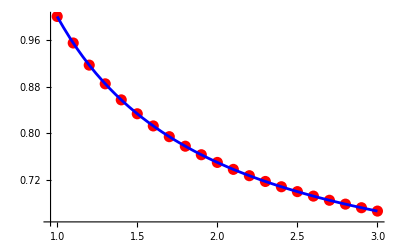

```mathematica
Show[plotvnum,plotvexact]
```

```mathematica
(*check w*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/w.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{3.,0.},{2.9,0.},{2.8,0.},{2.7,0.},{2.6,0.},{2.5,0.},{2.4,0.},{2.3,0.},{2.2,0.},{2.1,0.},{2.,0.},{1.9,0.},{1.8,0.},{1.7,0.},{1.6,0.},{1.5,0.},{1.4,0.},{1.3,0.},{1.2,0.},{1.1,0.},{1.,0.}}

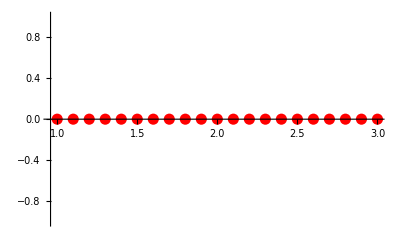

```mathematica
plotwnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

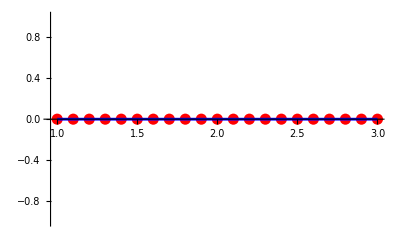

```mathematica
Show[plotwnum,plotwexact]
```

```mathematica
(*check sigma*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/sigma.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{3.,0.},{2.9,2.83252×10^-9},{2.8,3.13188×10^-9},{2.7,4.50451×10^-9},{2.6,6.14852×10^-9},{2.5,8.52068×10^-9},{2.4,1.18573×10^-8},{2.3,1.6641×10^-8},{2.2,2.35623×10^-8},{2.1,3.37753×10^-8},{2.,4.88623×10^-8},{1.9,7.23342×10^-8},{1.8,1.06455×10^-7},{1.7,1.6852×10^-7},{1.6,2.37784×10^-7},{1.5,4.7027×10^-7},{1.4,4.20455×10^-7},{1.3,2.03664×10^-6},{1.2,-1.51618×10^-6},{1.1,0.0000167299},{1.,-0.0000432611}}

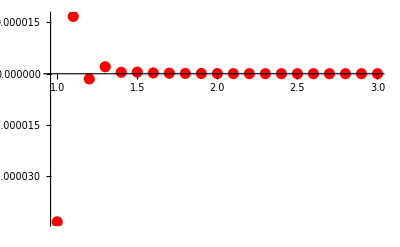

```mathematica
plotσnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

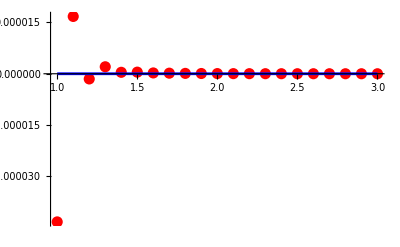

```mathematica
Show[plotσnum,plotσexact]
```

```mathematica
(*check ψ*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/psi.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{3.,2.},{2.9,1.8184},{2.8,1.61431},{2.7,1.39297},{2.6,1.16064},{2.5,0.924305},{2.4,0.69106},{2.3,0.467527},{2.2,0.259332},{2.1,0.0708002},{2.,-0.0951287},{1.9,-0.23679},{1.8,-0.353574},{1.7,-0.445672},{1.6,-0.513843},{1.5,-0.559231},{1.4,-0.583242},{1.3,-0.587474},{1.2,-0.57369},{1.1,-0.543824},{1.,-0.5}}

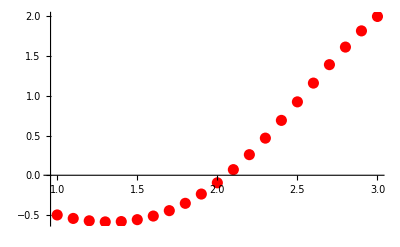

```mathematica
plotψnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

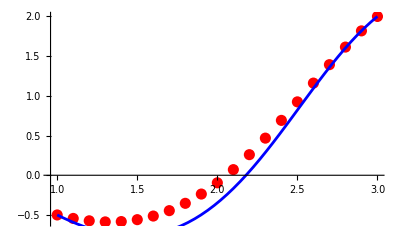

```mathematica
Show[plotψnum,plotψexact]
```

```mathematica
(*check X*)
```

```mathematica
tX=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/X.csv"];
tX=Table[{tX[[i,1]],tX[[i,2]]},{i,2,Length[tX]}]
```

{{0.859649,-0.209389},{0.884606,-0.139065},{0.895499,-0.0659232},{0.890717,0.00716379},{0.869798,0.0765851},{0.833686,0.138563},{0.78468,0.189825},{0.726038,0.228163},{0.661382,0.252703},{0.594105,0.263844},{0.526944,0.26295},{0.461797,0.251956},{0.399738,0.233001},{0.341159,0.208176},{0.285965,0.179378},{0.233759,0.148254},{0.184004,0.11621},{0.13615,0.0844319},{0.0897211,0.0539282},{0.0443864,0.0255494},{0.,0.}}

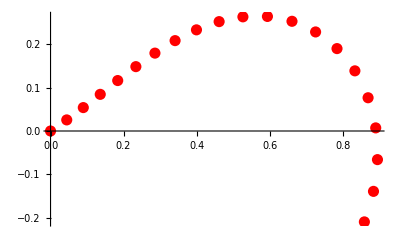

```mathematica
plotXnum=ListPlot[tX,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

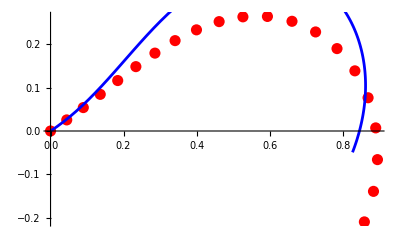

```mathematica
Show[plotXnum,plotXexact]
```